```mathematica
ExamineGraphs[from_,to_]:=Block[{},
Monitor[
Table[
Print["Starting ", p];
With[{mainGraph=Graph[plantri[[p]]]},
p->Table[
v->
{
ChromaticPolynomial[mainGraph,4]/24,

With[
{neighbours=VertexDelete[NeighborhoodGraph[mainGraph,v],v]},
With[{
span=FindSpanningTree[neighbours]
},
With[
{vert=TreeToCycle[span],
f=VertexDelete[EdgeDelete[mainGraph,EdgeList[neighbours]],v]},
Table[
With[
{i=EmbedGraphPlantri[f,h,vert]},
With[
{val=
ChromaticPolynomial[i,4]/24},
If[val==0,Print["OEPS--",p,"     ", v,"     ",vert, "     ", VertexList[span],"     ",EdgeList[span],"     ",h["signature"],"     ",Graph[i,GraphHighlight->vert,VertexLabels->"Name"],{ChromaticPolynomial[mainGraph,x],ChromaticPolynomial[f,x],ChromaticPolynomial[h["graph"],x],ChromaticPolynomial[i,x]}]
];
{val,Graph[VertexDelete[mainGraph,v],
GraphHighlight->EdgeList[neighbours],
GraphLayout->"PlanarEmbedding", 
VertexLabels->"Name",
PlotLabel->h["vertexsets"]/.Table[k->vert[[k]],{k,Length[vert]}]]}
]
]
,
{h,Table[stubbornForm5[k],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]}
]
]
]
]
}
,{v,Select[VertexList[mainGraph],VertexDegree[mainGraph,#]==5&](*Select[VertexList[mainGraph],VertexDegree[mainGraph,#]==5&]*)}
]
],
{p,from,to}
],
{p,v,h["signature"]}
]
]
```

Starting 8

Interrupted

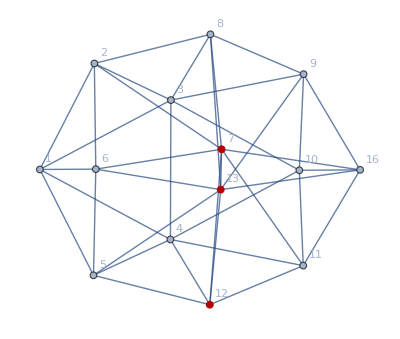
OEPS--8     14     {12,13,7,15,17}     {7,12,13,15,17}     {7<->13,7<->15,12<->13,15<->17}     29608     -Graphics-{71265972 x-351946840 x^2+802461675 x^3-1131475014 x^4+1112163274 x^5-812626569 x^6+458524982 x^7-204408959 x^8+72889503 x^9-20875904 x^10+4786421 x^11-868885 x^12+122328 x^13-12900 x^14+960 x^15-45 x^16+x^17,-686808 x+4062732 x^2-11179006 x^3+19059385 x^4-22586469 x^5+19749882 x^6-13182082 x^7+6843891 x^8-2787401 x^9+890524 x^10-221290 x^11+41986 x^12-5885 x^13+575 x^14-35 x^15+x^16,2 x-3 x^2+x^3,-2997216 x+12457536 x^2-23236766 x^3+26071339 x^4-19815666 x^5+10854453 x^6-4434668 x^7+1374444 x^8-324190 x^9+57590 x^10-7496 x^11+677 x^12-38 x^13+x^14}

Starting 9

Starting 10

Starting 11

Starting 12

Starting 13

Starting 14

Starting 15

```mathematica
values789Three=Monitor[
Table[
Print["Starting ", p];
With[{mainGraph=Graph[plantri[[p]]]},
p->Table[
v->
{
ChromaticPolynomial[mainGraph,4]/24,

With[
{neighbours=VertexDelete[NeighborhoodGraph[mainGraph,v],v]},
With[{
span=FindSpanningTree[neighbours]
},
With[
{vert=TreeToCycle[span],
f=VertexDelete[EdgeDelete[mainGraph,EdgeList[neighbours]],v]},
Table[
With[
{i=EmbedGraphPlantri[f,h,vert]},
With[
{val=
ChromaticPolynomial[i,4]/24},
If[val==0,Print["OEPS--",p,"     ", v,"     ",vert, "     ", VertexList[span],"     ",EdgeList[span],"     ",h["signature"],"     ",Graph[i,GraphHighlight->vert,VertexLabels->"Name"],{ChromaticPolynomial[mainGraph,x],ChromaticPolynomial[f,x],ChromaticPolynomial[h["graph"],x],ChromaticPolynomial[i,x]}]
];
{val,Graph[VertexDelete[mainGraph,v],
GraphHighlight->EdgeList[neighbours],
GraphLayout->"PlanarEmbedding", 
VertexLabels->"Name",
PlotLabel->h["vertexsets"]/.Table[k->vert[[k]],{k,Length[vert]}]]}
]
]
,
{h,Table[stubbornForm5[k],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]}
]
]
]
]
}
,{v,Select[VertexList[mainGraph],VertexDegree[mainGraph,#]==5&](*Select[VertexList[mainGraph],VertexDegree[mainGraph,#]==5&]*)}
]
],
{p,8,15}
],
{p,v,h["signature"]}
]
```

```mathematica
ExamineGraphs[16,20];
```

Starting 16

Starting 17

Starting 18

Starting 19

Starting 20

```mathematica
ExamineGraphs[21,22];
```

Starting 21

Starting 22

```mathematica
ExamineGraphs[23,25];
```

Starting 23

Starting 24

$Aborted